# Anscombe’s quartet

```mathematica
data="10.0	8.04	10.0	9.14	10.0	7.46	8.0	6.58
8.0	6.95	8.0	8.14	8.0	6.77	8.0	5.76
13.0	7.58	13.0	8.74	13.0	12.74	8.0	7.71
9.0	8.81	9.0	8.77	9.0	7.11	8.0	8.84
11.0	8.33	11.0	9.26	11.0	7.81	8.0	8.47
14.0	9.96	14.0	8.10	14.0	8.84	8.0	7.04
6.0	7.24	6.0	6.13	6.0	6.08	8.0	5.25
4.0	4.26	4.0	3.10	4.0	5.39	19.0	12.50
12.0	10.84	12.0	9.13	12.0	8.15	8.0	5.56
7.0	4.82	7.0	7.26	7.0	6.42	8.0	7.91
5.0	5.68	5.0	4.74	5.0	5.73	8.0	6.89";
```

```mathematica
summaryStatistics[points_]:=Grid[
{
{"mean of x values",Mean[points[[All,1]]]},
{"variance of x values",Variance[points[[All,1]]]},
{"mean of y values",Mean[points[[All,2]]]},
{"variance of y values",Variance[points[[All,2]]]},
{"correlation between x and y values",Correlation@@Transpose[points]}
},
Dividers-> All,
FrameStyle-> LightGray
]
```

```mathematica
$AnscombeQuartetData=Composition[
Transpose/@#&,
Partition[#,2]&,
Transpose,
Partition[#,8]&,
ToExpression/@#&,
StringSplit
][data]
```

{{{10.,8.04},{8.,6.95},{13.,7.58},{9.,8.81},{11.,8.33},{14.,9.96},{6.,7.24},{4.,4.26},{12.,10.84},{7.,4.82},{5.,5.68}},{{10.,9.14},{8.,8.14},{13.,8.74},{9.,8.77},{11.,9.26},{14.,8.1},{6.,6.13},{4.,3.1},{12.,9.13},{7.,7.26},{5.,4.74}},{{10.,7.46},{8.,6.77},{13.,12.74},{9.,7.11},{11.,7.81},{14.,8.84},{6.,6.08},{4.,5.39},{12.,8.15},{7.,6.42},{5.,5.73}},{{8.,6.58},{8.,5.76},{8.,7.71},{8.,8.84},{8.,8.47},{8.,7.04},{8.,5.25},{19.,12.5},{8.,5.56},{8.,7.91},{8.,6.89}}}

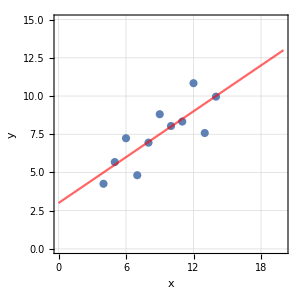
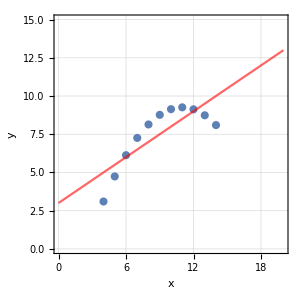
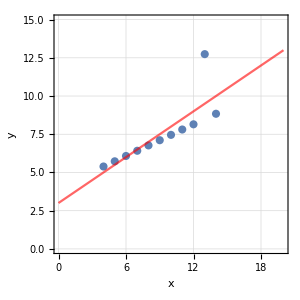
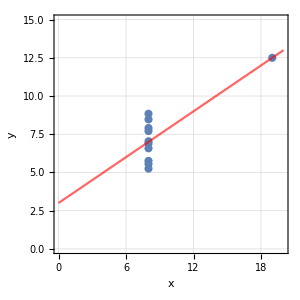
-Graphics-mean of x values | 9.
variance of x values | 11.
mean of y values | 7.50091
variance of y values | 4.12727
correlation between x and y values | 0.816421 | -Graphics-mean of x values | 9.
variance of x values | 11.
mean of y values | 7.50091
variance of y values | 4.12763
correlation between x and y values | 0.816237
-Graphics-mean of x values | 9.
variance of x values | 11.
mean of y values | 7.5
variance of y values | 4.12262
correlation between x and y values | 0.816287 | -Graphics-mean of x values | 9.
variance of x values | 11.
mean of y values | 7.50091
variance of y values | 4.12325
correlation between x and y values | 0.816521

```mathematica
Composition[
Grid[Partition[#,2](*,ImageSize-> 1000,PlotLabel-> "Anscombe's quartet"*)]&,
Labeled[
Show[
ListPlot[
#,
PlotRange-> {{0,20},{0,15}},
AspectRatio-> 1,
ImageSize-> 300,
Frame-> True,
GridLines-> Automatic,
FrameLabel-> {"x","y"}
],
With[{func=(a x + b) /.FindFit[#,a x + b, {a,b},x]},Plot[func,{x,0,20},PlotStyle-> {Opacity[0.6,Red]}]]
],
summaryStatistics[#]
]&/@#&
][$AnscombeQuartetData]
```